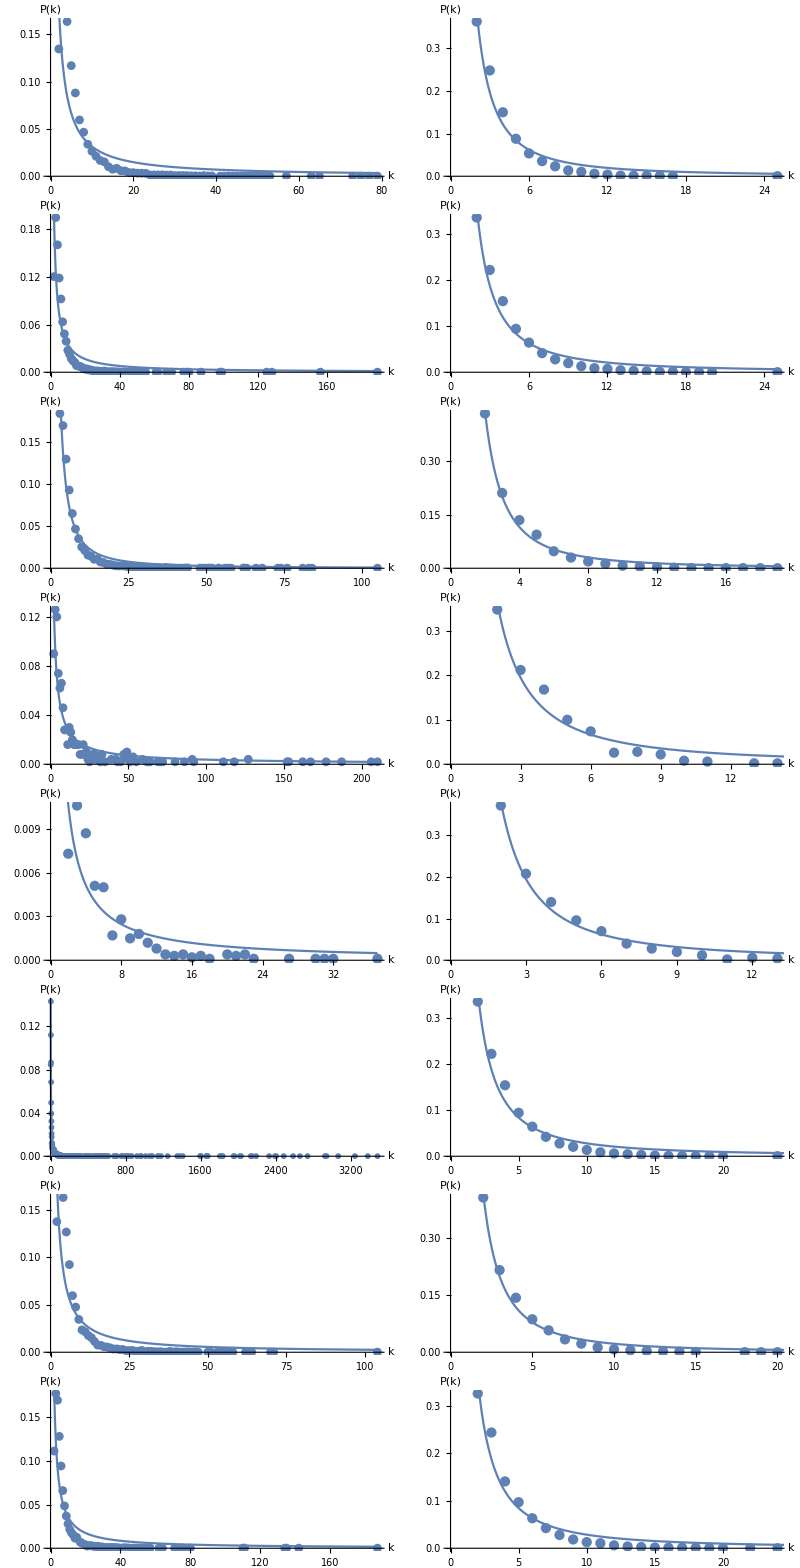
```mathematica
frame=-Graphics-;
```

```mathematica
visibility = frame[[1,All,1]];
```

```mathematica
horizontal = frame[[1,All,2]];
```

```mathematica
visibilityPoints=Cases[#,Point[data_]:>data,-4,1][[1]]&/@visibility;
```

```mathematica
horizontalPoints=Cases[#,Point[data_]:>data,-4,1][[1]]&/@horizontal;
```

```mathematica
LinearModelFit[Log@visibilityPoints[[1]],x,x]
```

FittedModel[2.1772-2.71055 x]

```mathematica
AppendTo[horizontalPoints,{{2,3493/9999},{4,1490/9999},{3,766/3333},{5,29/303},{6,607/9999},{7,4/99},{8,259/9999},{9,170/9999},{11,7/909},{12,38/9999},{13,7/3333},{14,17/9999},{15,2/1111},{17,4/9999},{10,127/9999},{16,1/1111},{20,4/9999},{18,1/3333},{19,1/9999}}];
```

```mathematica
AppendTo[visibilityPoints,{{181,4/9999},{182,1/1111},{184,1/9999},{172,1/9999},{162,1/9999},{160,2/9999},{289,1/9999},{111,8/9999},{117,14/9999},{114,7/9999},{120,7/9999},{115,8/9999},{123,4/9999},{112,1/909},{107,2/3333},{294,1/9999},{96,1/909},{100,4/3333},{110,7/9999},{94,1/909},{106,5/9999},{109,2/3333},{113,1/1111},{116,1/3333},{118,7/9999},{325,2/9999},{98,7/9999},{95,1/909},{105,1/1111},{103,8/9999},{92,2/3333},{259,1/9999},{102,8/9999},{350,1/9999},{99,7/9999},{97,1/1111},{108,4/3333},{104,2/3333},{93,5/9999},{101,5/9999},{127,5/9999},{384,1/9999},{79,14/9999},{64,14/9999},{84,14/9999},{71,25/9999},{82,14/9999},{54,14/3333},{67,26/9999},{57,1/303},{56,4/1111},{53,53/9999},{698,1/9999},{47,70/9999},{59,29/9999},{38,158/9999},{943,1/9999},{58,4/1111},{39,131/9999},{66,20/9999},{55,38/9999},{76,2/909},{69,16/9999},{63,2/1111},{41,10/909},{78,7/9999},{868,1/9999},{34,131/9999},{50,20/3333},{46,65/9999},{51,20/3333},{36,19/1111},{1389,1/9999},{75,23/9999},{33,124/9999},{35,50/3333},{37,175/9999},{44,10/1111},{45,20/3333},{1728,1/9999},{1634,1/9999},{40,131/9999},{30,89/9999},{8,287/9999},{5,19/303},{25,1/303},{12,164/9999},{11,65/3333},{31,29/3333},{6,500/9999},{26,5/1111},{20,94/9999},{16,35/3333},{3,1024/9999},{4,745/9999},{10,82/3333},{19,70/9999},{23,2/303},{21,82/9999},{15,107/9999},{14,10/909},{17,91/9999},{2,199/3333},{2293,1/9999},{48,23/3333},{22,23/3333},{18,32/3333},{13,13/1111},{9,83/3333},{7,41/1111},{24,16/3333},{29,71/9999},{28,82/9999},{164,1/9999},{187,1/9999},{183,4/9999},{179,1/9999},{190,2/9999},{177,1/9999},{186,1/9999},{188,1/9999},{195,1/9999},{175,1/9999},{171,1/9999},{255,1/3333},{231,2/9999},{169,1/9999},{81,19/9999},{453,1/9999},{193,1/9999},{90,16/9999},{88,2/9999},{91,4/3333},{280,1/9999},{62,25/9999},{254,2/9999},{89,1/1111},{77,1/909},{455,1/9999},{83,4/3333},{60,2/909},{52,49/9999},{85,1/1111},{86,5/3333},{119,2/3333},{87,8/9999},{74,2/909},{121,2/9999},{359,2/9999},{625,1/9999},{602,1/9999},{65,23/9999},{32,85/9999},{200,1/9999},{207,1/9999},{209,1/9999},{140,1/3333},{72,19/9999},{70,2/909},{122,5/9999},{73,17/9999},{42,94/9999},{68,20/9999},{221,1/9999},{138,4/9999},{61,20/9999},{735,1/9999},{1766,1/9999},{135,2/9999},{139,1/3333},{49,59/9999},{658,1/9999},{134,4/9999},{131,2/9999},{409,1/9999},{498,1/9999},{366,1/9999},{487,1/9999},{508,1/9999},{533,1/9999},{407,1/9999},{480,1/9999},{422,1/9999},{512,1/9999},{559,1/9999},{490,1/9999},{563,1/9999},{303,1/9999},{143,1/3333},{146,1/9999},{465,1/9999},{592,1/9999},{348,1/9999},{206,1/9999},{320,1/9999},{201,1/9999},{212,2/9999},{214,1/9999},{942,1/9999},{643,1/9999},{220,1/9999},{232,1/9999},{448,1/9999},{328,1/9999},{125,2/9999},{851,1/9999},{1400,1/9999},{803,1/9999},{154,1/3333},{241,1/9999},{43,82/9999},{155,2/9999},{129,4/9999},{784,1/9999},{266,1/9999},{80,17/9999},{599,1/9999},{128,4/9999},{130,1/3333},{397,1/9999},{751,1/9999},{152,1/9999},{1130,1/9999},{203,1/9999},{793,2/9999},{1343,1/9999},{665,1/9999},{238,1/9999},{543,1/9999},{415,1/9999},{669,1/9999},{202,1/9999},{996,1/9999},{204,1/9999},{1015,1/9999},{824,2/9999},{389,1/9999},{249,1/9999},{940,1/9999},{132,1/9999},{133,1/9999},{855,1/9999},{1553,1/9999},{151,2/9999},{347,1/9999},{198,1/9999},{774,1/9999},{1068,1/9999},{649,1/9999},{240,1/9999},{351,1/9999},{383,1/9999},{136,1/9999},{491,1/9999},{659,1/9999},{230,2/9999},{1612,1/9999},{235,1/9999},{1157,1/9999},{147,2/9999},{194,1/9999},{159,1/9999},{148,1/9999},{1477,1/9999},{1348,1/9999},{145,1/3333},{124,2/9999},{156,1/9999},{229,1/9999},{126,1/9999},{1920,1/9999},{1203,1/9999},{27,53/9999},{1670,1/9999},{1153,1/9999},{1223,1/9999},{1336,1/9999},{153,1/3333},{1542,1/9999},{375,1/9999},{191,1/9999},{349,1/9999},{144,1/9999},{1083,1/9999},{520,1/9999},{142,1/9999},{982,1/9999},{1485,1/9999},{948,1/9999},{199,2/9999},{2307,1/9999},{1429,1/9999},{1494,1/9999},{944,1/9999},{1740,1/9999},{1806,1/9999},{1148,1/9999},{936,1/9999},{1921,1/9999},{150,1/9999},{1759,2/9999},{2348,1/9999},{1973,1/9999},{2125,1/9999},{2410,1/9999},{2343,1/9999},{2070,1/9999},{1885,1/9999},{2474,1/9999},{2347,1/9999},{211,1/9999},{137,2/9999},{700,1/9999},{2175,1/9999},{1387,1/9999},{2315,1/9999},{1720,1/9999},{1915,1/9999},{1587,1/9999},{2094,1/9999},{958,1/9999},{1819,1/9999},{2266,1/9999},{1258,1/9999},{1708,2/9999},{1648,2/9999},{2145,1/9999},{1599,1/9999},{1419,1/9999},{1651,1/9999},{1799,1/9999},{1772,1/9999},{1659,1/9999},{766,1/9999},{1894,1/9999},{1770,1/9999},{1661,1/9999},{1471,1/9999},{1562,1/9999},{1705,1/9999},{1726,1/9999},{224,1/9999},{1567,1/9999},{189,1/9999},{1908,1/9999},{1180,1/9999},{1686,1/9999},{2144,1/9999},{2451,1/9999},{1660,1/9999},{1675,1/9999},{1919,1/9999},{1787,1/9999},{1752,1/9999},{1559,1/9999},{1848,1/9999},{1711,1/9999},{1769,1/9999},{1546,1/9999},{1667,1/9999},{1665,1/9999},{1853,1/9999},{1715,1/9999},{1589,1/9999},{1603,1/9999},{1706,1/9999}}];
```

```mathematica
AppendTo[horizontalPoints,{{2,179/500},{3,111/500},{5,21/250},{4,93/500},{6,19/250},{8,13/500},{9,1/100},{7,3/125},{10,1/250},{11,1/250},{12,1/500}}];
```

```mathematica
#[[1]]->#[[2]]&/@Transpose@{Table[x,{x,10}],Table[x^2, {x,10}]}
```

{1→1,2→4,3→9,4→16,5→25,6→36,7→49,8→64,9→81,10→100}

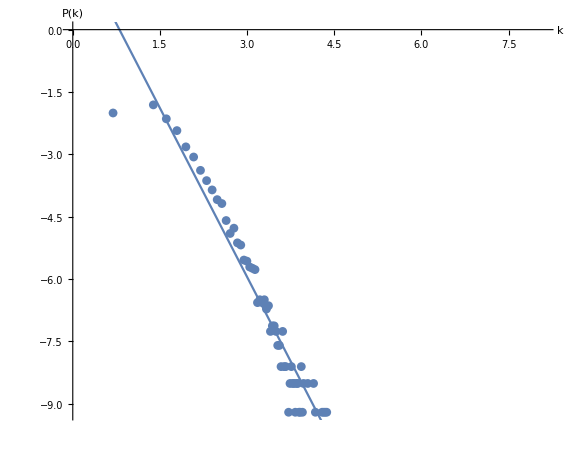
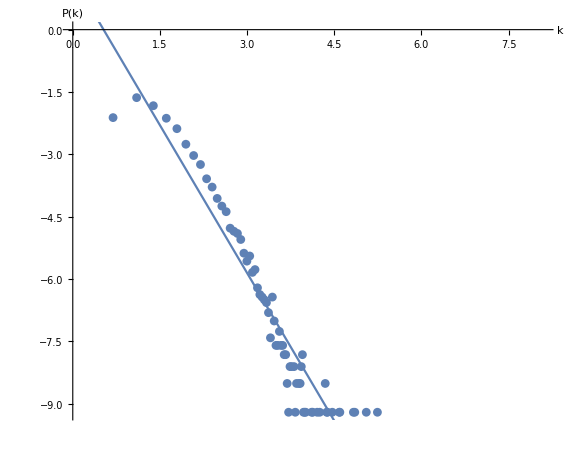
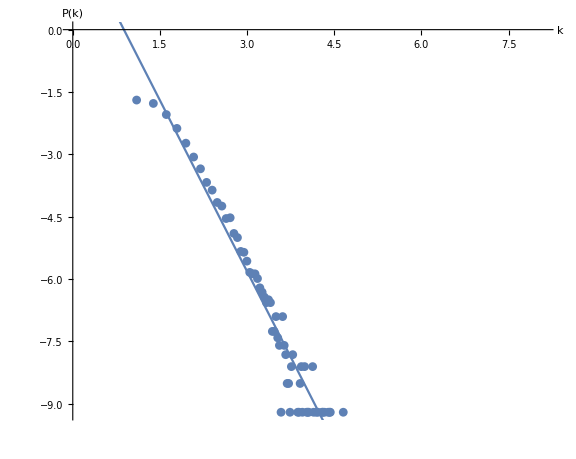
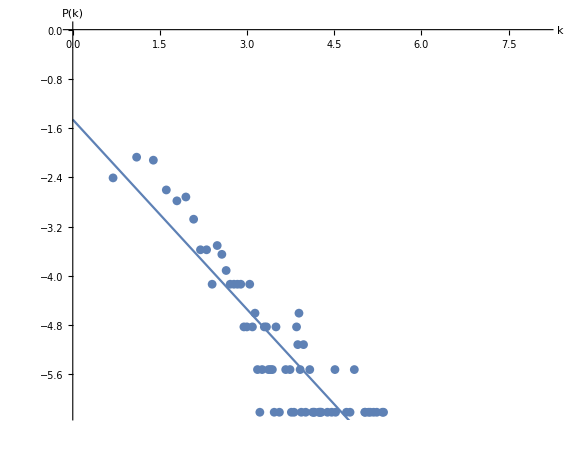
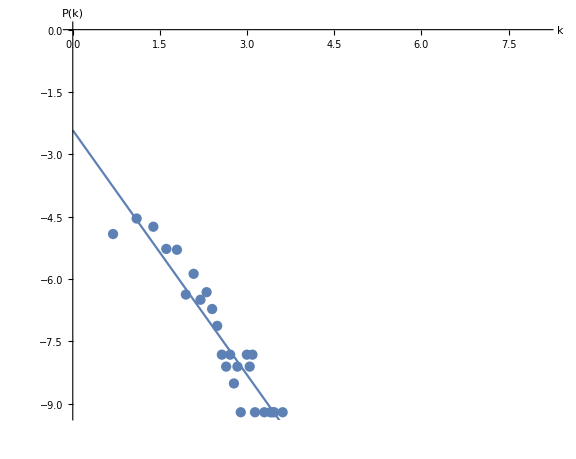
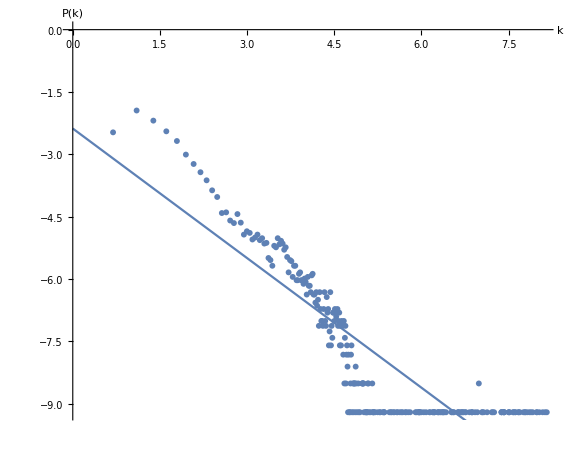
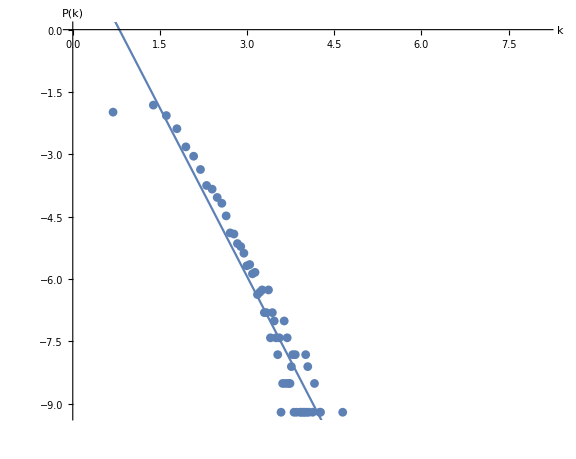
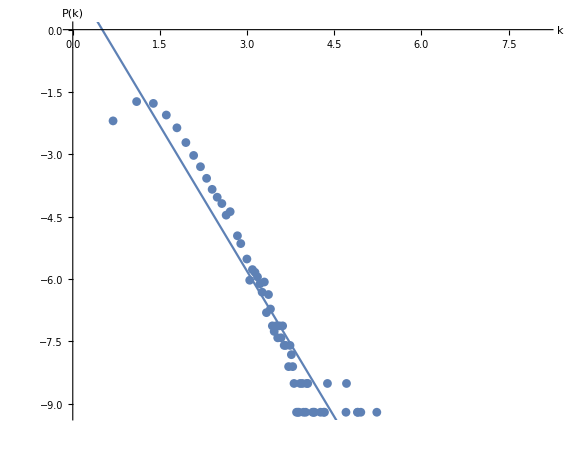
{-Graphics-d=2,-Graphics-d=3,-Graphics-d=4,-Graphics-d=5,-Graphics-d=6,-Graphics-d=7,-Graphics-d=8,-Graphics-d=9,-Graphics-d=10,-Graphics-d=11}

```mathematica
visibilityPlots=(
lm=LinearModelFit[Log@#[[1]],x,x];
Labeled[Show[
ListPlot[Log@#[[1]],PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
Plot[lm[x],{x,0,8.1},PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large,AspectRatio->0.8
],Style[#[[2]],38],Top])&/@Transpose@{visibilityPoints,{"d=2","d=3","d=4","d=5","d=6","d=7","d=8","d=9","d=10","d=11"}}
```

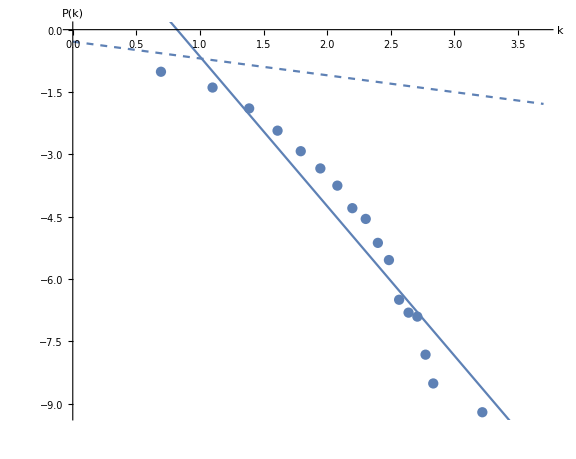
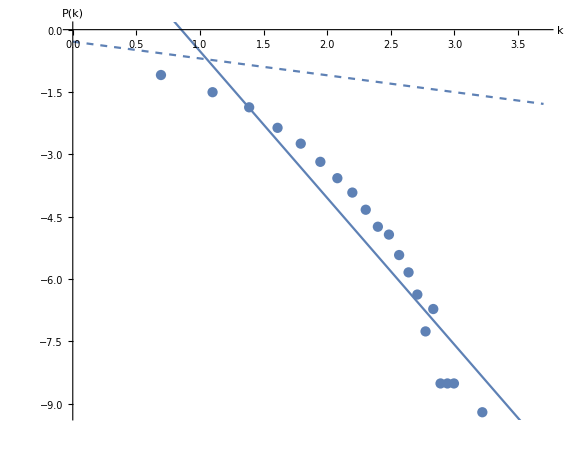
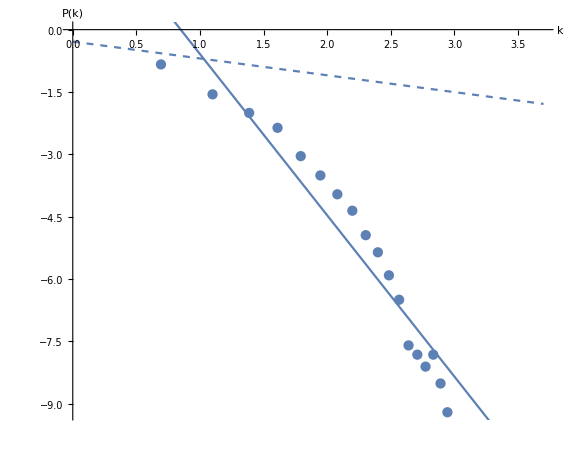
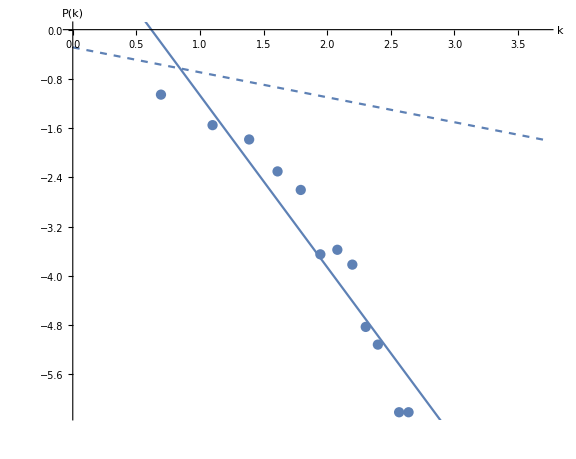
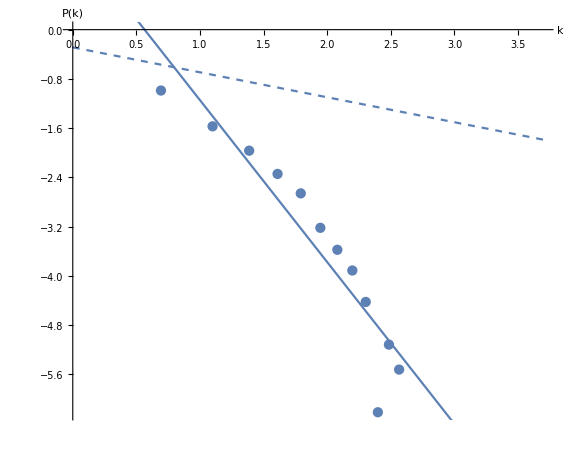
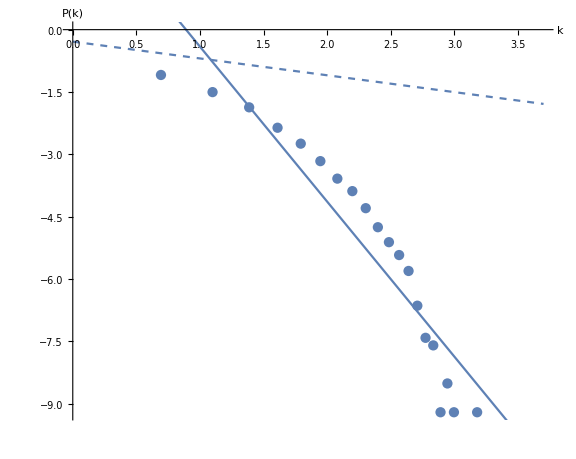
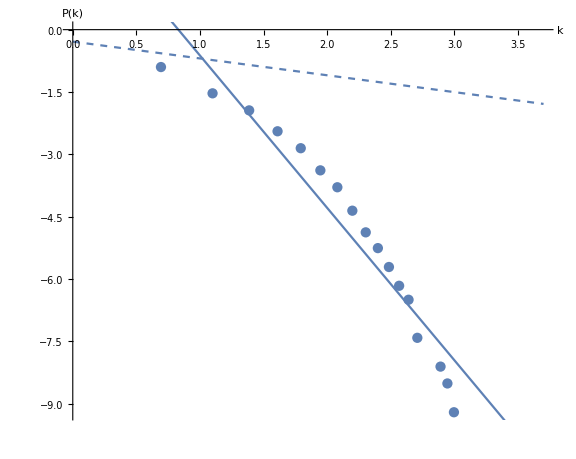
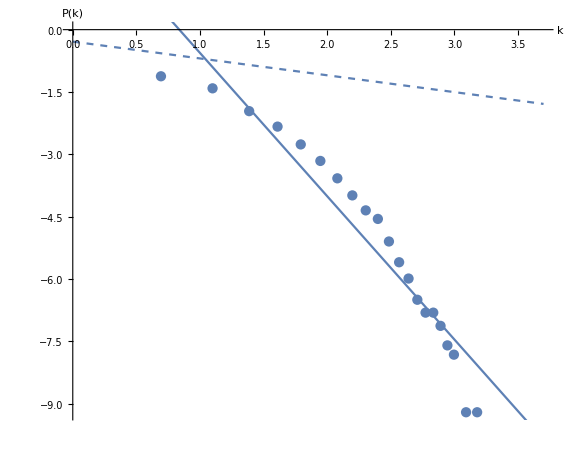
{-Graphics-d=2,-Graphics-d=3,-Graphics-d=4,-Graphics-d=5,-Graphics-d=6,-Graphics-d=7,-Graphics-d=8,-Graphics-d=9,-Graphics-d=10,-Graphics-d=11}

```mathematica
horizontalPlots=(
lm=LinearModelFit[Log@#[[1]],x,x];
fm=1/3(2/3)^(#-2)&;
Labeled[Show[
ListPlot[Log@#[[1]],PlotRange->{{0,3.7},All},AxesOrigin->{0,0}],
Plot[lm[x],{x,0,3.7},PlotRange->{{0,3.7},All},AxesOrigin->{0,0}],
Plot[Log@fm[x],{x,0,3.7},PlotRange->{{0,3.7},All},AxesOrigin->{0,0},PlotStyle->Dashed],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large,AspectRatio->0.8
],Style[#[[2]],38],Top])&/@Transpose@{horizontalPoints,{"d=2","d=3","d=4","d=5","d=6","d=7","d=8","d=9","d=10","d=11"}}
```

```mathematica
Export["natural-2.eps",visibilityPlots[[1]]];
Export["horizontal-2.eps",horizontalPlots[[1]]];
Export["naturalGrid.eps", Grid[Partition[visibilityPlots,2],Spacings->{Automatic,4}]];
Export["horizontalGrid.eps", Grid[Partition[horizontalPlots,2],Spacings->{Automatic,4}]];
```

## d = 10

### visibility

```mathematica
countrel={{2,1325/9999},{5,1247/9999},{3,1985/9999},{7,598/9999},{13,14/909},{19,14/3333},{4,1619/9999},{9,359/9999},{8,469/9999},{11,71/3333},{6,844/9999},{17,62/9999},{18,6/1111},{25,14/9999},{15,106/9999},{10,82/3333},{14,127/9999},{31,13/9999},{12,58/3333},{23,7/3333},{22,28/9999},{24,17/9999},{61,1/9999},{26,19/9999},{16,76/9999},{37,5/9999},{21,32/9999},{43,2/9999},{46,4/9999},{48,4/9999},{73,1/9999},{28,5/3333},{33,4/3333},{29,5/9999},{20,41/9999},{27,10/9999},{30,8/9999},{39,5/9999},{38,5/9999},{36,7/9999},{35,1/3333},{34,4/9999},{32,4/9999},{40,1/3333},{45,1/9999},{53,2/9999},{60,2/9999},{74,1/9999},{65,1/9999},{87,1/9999},{42,1/3333},{47,1/9999},{57,1/9999},{44,1/9999},{54,1/9999}};
```

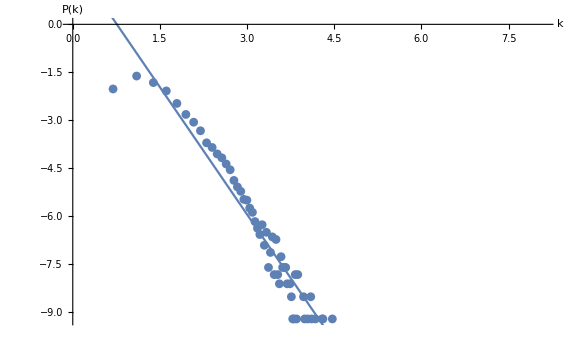

```mathematica
(lm=LinearModelFit[Log@#,x,x];
Show[
ListPlot[Log@#,PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
Plot[lm[x],{x,0,8.1},PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
])&@countrel
```

```mathematica
results={};
```

```mathematica
degree=VertexDegree[igv10]//Mean//N
```

6.23062

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.438508/x^1.09623]

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

```mathematica
results
```

{{visibility,10,9999,6.23062,1.09623 ± 0.187463,0.438508 ± 0.117337}}

```mathematica
Export["v10.eps",-Graphics-]
```

v10.eps

### horizontal visibility

```mathematica
countrel={{2,3493/9999},{4,1490/9999},{3,766/3333},{5,29/303},{6,607/9999},{7,4/99},{8,259/9999},{9,170/9999},{11,7/909},{12,38/9999},{13,7/3333},{14,17/9999},{15,2/1111},{17,4/9999},{10,127/9999},{16,1/1111},{20,4/9999},{18,1/3333},{19,1/9999}};
```

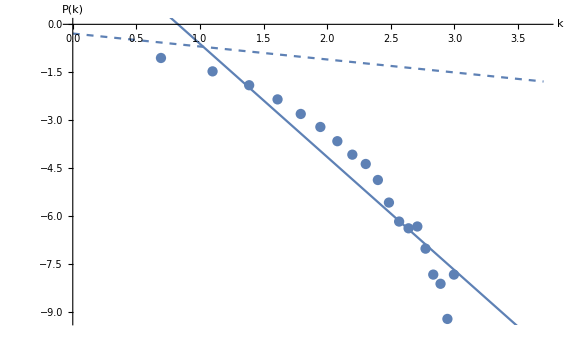

```mathematica
(
lm=LinearModelFit[Log@#,x,x];
fm=1/3(2/3)^(#-2)&;
Show[
ListPlot[Log@#,PlotRange->{{0,3.7},All},AxesOrigin->{0,0}],
Plot[lm[x],{x,0,3.7},PlotRange->{{0,3.7},All},AxesOrigin->{0,0}],
Plot[Log@fm[x],{x,0,3.7},PlotRange->{{0,3.7},All},AxesOrigin->{0,0},PlotStyle->Dashed],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
])&@countrel
```

```mathematica
Export["h10.eps",-Graphics-]
```

h10.eps

```mathematica
degree=VertexDegree[igh10]//Mean//N
```

3.84218

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[1.1457/x^1.62678]

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

```mathematica
results//TableForm
```

visibility | 10 | 9999 | 6.23062 | 1.09623 ± 0.187463 | 0.438508 ± 0.117337
visibility | 10 | 9999 | 3.84218 | 1.62678 ± 0.206643 | 1.1457 ± 0.237232

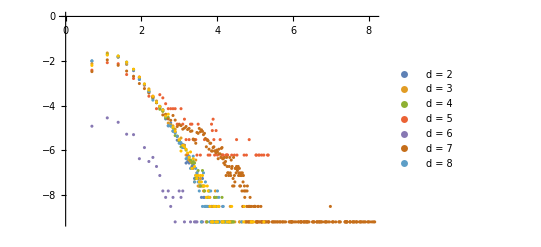

```mathematica
ListPlot[Log@visibilityPoints,PlotRange->{{0,8.1},All},AxesOrigin->{0,0},PlotLegends->{"d = 2","d = 3","d = 4","d = 5","d = 6","d = 7","d = 8"}]
```

```mathematica
lms=LinearModelFit[Log@#,x,x][y]&/@visibilityPoints
```

{2.1772-2.71055 y,1.25734-2.37216 y,2.4161-2.7461 y,-1.46055-1.02792 y,-2.42184-1.96406 y,-2.3801-1.03996 y,2.16589-2.70372 y,1.18409-2.33426 y}

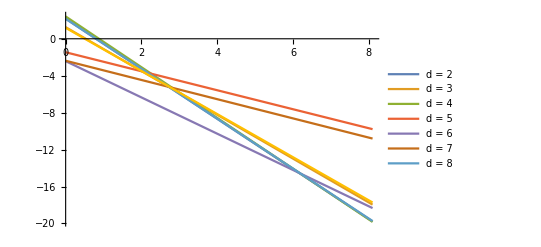

```mathematica
Plot[{2.1771995170383946-2.7105522658721974 y,1.2573403955105085-2.37216020084492 y,2.4161030852343557-2.7460957230348537 y,-1.460545067175454-1.0279248355706383 y,-2.421840496243267-1.9640589793665224 y,-2.3801019198021014-1.0399614466205362 y,2.16588703016536-2.703716924005051 y,1.18409246190788-2.3342645616459414 y},{y,0,8.1},PlotRange->{{0,8.1},All},AxesOrigin->{0,0},
PlotLegends->{"d = 2","d = 3","d = 4","d = 5","d = 6","d = 7","d = 8"}]
```

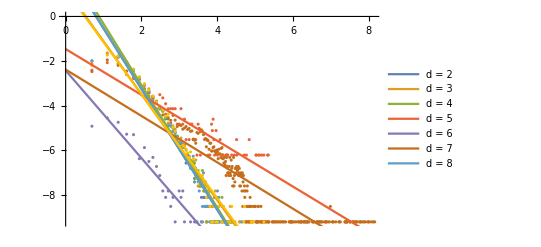

```mathematica
Show[
ListPlot[Log@visibilityPoints,PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
Plot[lms,{y,0,8.1},PlotRange->{{0,8.1},All},AxesOrigin->{0,0},
PlotLegends->{"d = 2","d = 3","d = 4","d = 5","d = 6","d = 7","d = 8"}]
]
```

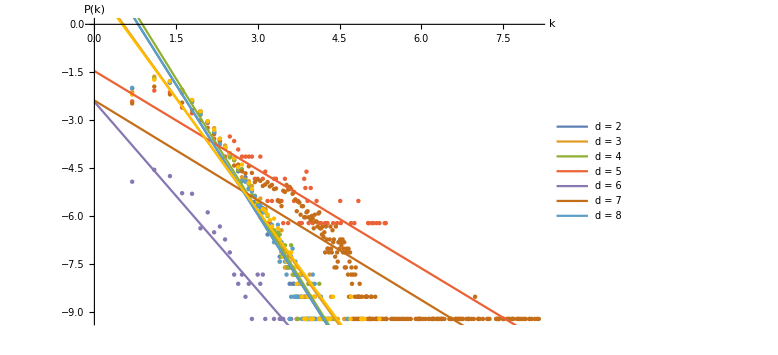

```mathematica
Show[
ListPlot[Log@visibilityPoints,PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
Plot[lms,{y,0,8.1},PlotRange->{{0,8.1},All},AxesOrigin->{0,0},
PlotLegends->{"d = 2","d = 3","d = 4","d = 5","d = 6","d = 7","d = 8"}]
,
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export["graph.pdf", %%]
```

graph.pdf

## d=11